## New Plots for the excitation energies in 163Lu

```mathematica
ClearAll["Global`*"]
```

```mathematica
path[filename_]:=StringTemplate["/Users/basavyr/Documents/Work/PhD/163Lu-New-TSD4-Formalism/Code/Update-July-2022/plots/``"][filename];
export[filename_,obj_]:=Export[path[filename],Show[obj]];
```

### TSD1

```mathematica
spins1={8.5,10.5,12.5,14.5,16.5,18.5,20.5,22.5,24.5,26.5,28.5,30.5,32.5,34.5,36.5,38.5,40.5,42.5,44.5,46.5,48.5};
band1Exp={0.1966,0.4597,0.7746,1.1609,1.6112,2.1265,2.7051,3.3441,4.0411,4.7937,5.5992,6.457,7.3667,8.3293,9.3458,10.4169,11.5431,12.7224,13.9491,15.2181,16.5221};
band1Th={0.230329,0.516162,0.857522,1.25441,1.70683,2.21478,2.77826,3.39726,4.07178,4.80183,5.5874,6.42849,7.3251,8.27724,9.28491,10.3481,11.4668,12.6411,13.8708,15.1561,16.497};
```

### TSD2

```mathematica
spins2={13.5,15.5,17.5,19.5,21.5,23.5,25.5,27.5,29.5,31.5,33.5,35.5,37.5,39.5,41.5,43.5,45.5};
band2Exp={1.3394,1.7467,2.2184,2.7527,3.3484,4.003,4.7143,5.4805,6.3004,7.1733,8.0998,9.08,10.1147,11.2036,12.3466,13.5441,14.7911};
band2Th={1.34903,1.77368,2.25387,2.78958,3.38082,4.02758,4.72986,5.48767,6.301,7.16986,8.09423,9.07413,10.1096,11.2005,12.347,13.549,14.8065};
```

### TSD3

```mathematica
spins3={16.5,18.5,20.5,22.5,24.5,26.5,28.5,30.5,32.5,34.5,36.5,38.5,40.5,42.5};
band3Exp={2.1237,2.6293,3.1973,3.8243,4.5094,5.2506,6.0465,6.8963,7.7988,8.7546,9.7638,10.8268,11.9392,13.0861};
band3Th={2.04238,2.57396,3.15888,3.7974,4.48976,5.23613,6.0367,6.89161,7.80099,8.76495,9.7836,10.857,11.9853,13.1685};
```

### TSD4

```mathematica
spins4={23.5,25.5,27.5,31.5,33.5,35.5,37.5,39.5,41.5};
band4Exp={4.58,5.2251,5.9273,6.6819,7.4919,8.3573,9.2778,10.2535,11.2851,12.3701};
band4Th={4.32758,5.02986,5.78767,6.601,7.46986,8.39423,9.37413,10.4096,11.5005,12.647};
```

```mathematica
expPlot[expdata_]:=ListLinePlot[Table[{{1,expdata[[i]]},{2,expdata[[i]]}},{i,1,Length[expdata]}],AspectRatio->1.5,ImageSize->380,Frame->{{True,True},{True,True}},Axes->False,PlotStyle->Directive[Black,Thick],FrameStyle->Directive[Black,Thick],FrameLabel->{None,"E_exc [MeV]"},LabelStyle->{20,Bold,Black,FontFamily->"Arial"},FrameTicks->{{Table[i,{i,0,Round[Max[expdata]]+2,2}],Table[i,{i,0,Round[Max[expdata]]+2,2}]},{None,None}}];
thPlot[thdata_,linecolor_]:=ListLinePlot[Table[{{2.5,thdata[[i]]},{3.5,thdata[[i]]}},{i,1,Length[thdata]}],AspectRatio->1.5,ImageSize->380,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->Directive[linecolor,Thick]];
```

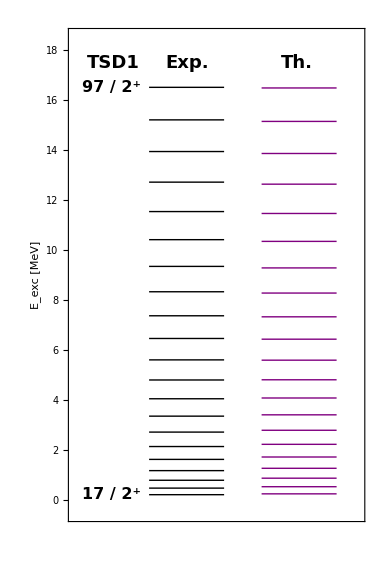

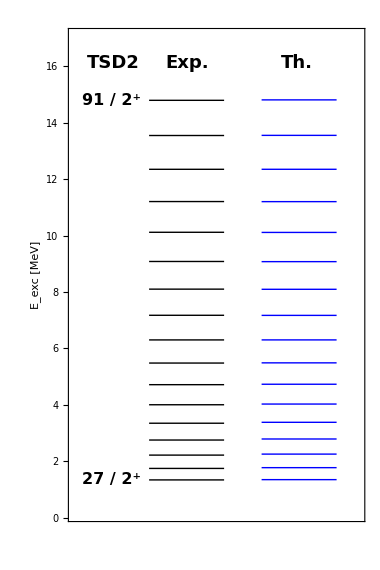

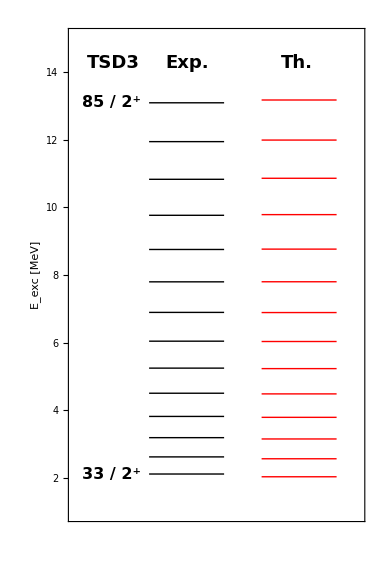

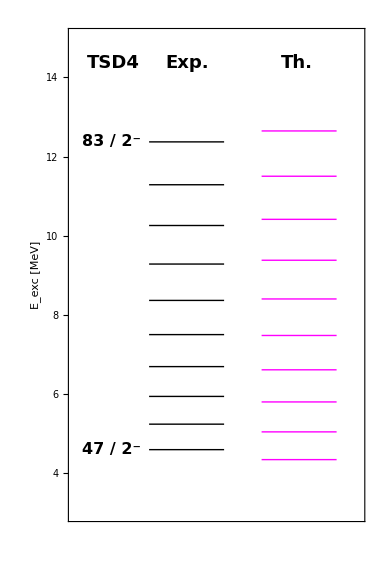

```mathematica
lineplot[data1_,data2_,xrange_,yrange_,thcolor_,spins_,parity_,label_]:=Show[{expPlot[data1],thPlot[data2,thcolor]},PlotRange->{xrange,yrange},Epilog->{ Inset[Style[StringTemplate["``"][label],18,Bold,Black,FontFamily->"Arial"],Scaled[{0.15,0.93}]],Inset[Style[StringTemplate["`` / 2^(``)"][Round[2*spins[[1]]],parity],16,Bold,Black,FontFamily->"Arial"],{0.5,data1[[1]]}], Inset[Style[StringTemplate["`` / 2^(``)"][Round[2*spins[[-1]]],parity],16,Bold,Black,FontFamily->"Arial"],{0.5,data1[[-1]]}], Inset[Style["Exp.",18,Italic,Black,Bold,FontFamily->"Arial"],Scaled[{0.4,0.93}]],Inset[Style["Th.",18,Italic,Black,Bold,FontFamily->"Arial"],Scaled[{0.77,0.93}]]}];
tsd1plot=lineplot[band1Exp,band1Th,{0,3.8},{-0.5,18.5},Purple,spins1,"+","TSD1"];
tsd2plot=lineplot[band2Exp,band2Th,{0,3.8},{0.2,17},Blue,spins2,"+","TSD2"];
tsd3plot=lineplot[band3Exp,band3Th,{0,3.8},{1,15},Red,spins3,"+","TSD3"];
tsd4plot=lineplot[band4Exp,band4Th,{0,3.8},{3,15},Magenta,spins4,"-","TSD4"];
Show[tsd1plot]
export["tsd1.pdf",tsd1plot];
Show[tsd2plot]
export["tsd2.pdf",tsd2plot];
Show[tsd3plot]
export["tsd3.pdf",tsd3plot];
Show[tsd4plot]
export["tsd4.pdf",tsd4plot];
```